```mathematica
Pane[Grid[{
{Style["Simulation of HG with salt effects thermodynamics","Chapter"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Simulation of HG with salt effects thermodynamics
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];
(*set values*)
h0fixed=1; d0fixed=1;kequhdfixed=2;kequhgafixed=2;sighdfixed=1;sigdfixed=1;sig0fixed=1;
h0error=0; d0error=0;kequhderror=0;kequhgaerror=0;sighderror=0;sigderror=0;sig0error=0;
(* Load Packges*)	
	
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHD-SE2.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHD.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
(* Paths*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-thermoHGSE2.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-thermoHGSE2.mx"}];

initialparameters=Import[defaultPath];
	h0in=initialparameters[[1]];
	d0in=initialparameters[[2]];
	step=initialparameters[[3]];
	kequhdin=initialparameters[[4]];
	sig0in=initialparameters[[5]];
	sigdin=initialparameters[[6]];
	sighdin=initialparameters[[7]];
	sa0in=initialparameters[[8]];
	kequhsain=initialparameters[[9]];
	sb0in=initialparameters[[10]];
	kequhsbin=initialparameters[[11]];

(*Buttons
*)simulationbutton=MouseAppearance[Button["Simulate",{ nb=EvaluationNotebook[],NotebookFind[nb,"simroutineHDSE1",All,CellTags],SelectionEvaluate[nb]},BaseStyle->EdgeForm[Dotted]],"LinkHand"];
variablessavebutton=MouseAppearance[Button["Save Parameters",{
initialparameters={
h0in,
d0in,
step,
kequhdin,
sig0in,
sigdin,
sighdin,
sa0in,
kequhsain,
sb0in,
kequhsbin
},Export[tempPath,initialparameters]},Appearance->"DialogBox"],"LinkHand"];
variablesloadbutton=MouseAppearance[Button["Load Saved Parameters",{
initialparameters=Import[tempPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	sa0in=initialparameters[[8]],
	kequhsain=initialparameters[[9]],
	sb0in=initialparameters[[10]],
	kequhsbin=initialparameters[[11]]
	},Appearance->"DialogBox"],"LinkHand"];

defaultloadbutton=MouseAppearance[Button["Load Default Parameters",{
initialparameters=Import[defaultPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	sa0in=initialparameters[[8]],
	kequhsain=initialparameters[[9]],
	sb0in=initialparameters[[10]],
	kequhsbin=initialparameters[[11]]
	},Appearance->"DialogBox"],"LinkHand"];

inputline = {
   {
   Style["species", Bold,Underlined, FontSize->12 ,TextAlignment->Right], 
   Style["concentration", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"",
   Style["binding", Bold,Underlined, FontSize->12 ,TextAlignment->Right]},

   {
   Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 6],"M",
Style["c-step ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[step], FieldSize -> 6],"M"},
 {"",Dynamic[h0in*1000000],"μM","c-step","","",""},
 
 {Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right], 
   InputField[Dynamic[d0in], FieldSize -> 6],"M",Style["K_equ(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhdin], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhdin]],""},
 
 
 
   {Style["Salt A:", Bold, FontSize->16 ,TextAlignment->Right], 
      InputField[Dynamic[sa0in], FieldSize -> 6],"M",Style["K_equ(HS_A)" , Bold, FontSize->16 ,TextAlignment->Right],
      InputField[Dynamic[kequhsain], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[sa0in*1000],"mM","lg(K_equ)",Dynamic[Log10[kequhsain]],""},
   
    {Style["Salt B:", Bold, FontSize->16 ,TextAlignment->Right], 
      InputField[Dynamic[sb0in], FieldSize -> 6],"M",Style["K_equ(HS_B)" , Bold, FontSize->16 ,TextAlignment->Right],
      InputField[Dynamic[kequhsbin], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[sb0in*1000],"mM","lg(K_equ)",Dynamic[Log10[kequhsbin]],""},
   
   
   {Style["Signal-HD", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 6],"",
   
   Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 6],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 6]},
      {"HD complex","","","dye alone","","","Startsignal"}  
    
};
kequhdout=kequhdin;
fitteddata={};
Print[TableForm[{{simulationbutton,variablesloadbutton,variablessavebutton,defaultloadbutton}}]];

Print[TableForm[inputline, TableAlignments -> Left]];
Print[Style["Salt - ",Bold],Style["Environmental disturbance of the binding of Host and Guest. Salts are interpreted to compete for the host with a weak affinity at high concentrations",Italic,Bold,FontColor->Gray]];
```

Simulate | Load Saved Parameters | Save Parameters | Load Default Parameters

species | concentration |  | binding |  |  |  | 
Host: |  | M | c-step  |  | M |  | 
 |  | μM | c-step |  |  |  | 
Dye: |  | M | K_equ(HD) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Salt A: |  | M | K_equ(HS_A) |  | M^-1 |  | 
 |  | mM | lg(K_equ) |  |  |  | 
Salt B: |  | M | K_equ(HS_B) |  | M^-1 |  | 
 |  | mM | lg(K_equ) |  |  |  | 
Signal-HD |  |  | Signal-D |  |  | Signal-0 | 
HD complex |  |  | dye alone |  |  | Startsignal |

Salt - Environmental disturbance of the binding of Host and Guest. Salts are interpreted to compete for the host with a weak affinity at high concentrations

```mathematica
Off[Export::chtype];
Off[First::nofirst];
mode="H0 varied";




datasignal=sthdse2SignalData[kequhdin,kequhsain,kequhsbin,h0in,d0in,sa0in,sb0in,sig0in,sighdin,sigdin,step];

inputs={{"Quantity","Value"},
{"Mode",mode},
{"conc(H)",h0in},
{"conc(D)",d0in},
{"Kequ(HD)",kequhdin},
{"conc(Sa)",sa0in},
{"Kequ(HSa)",kequhsain},
{"conc(Sa)",sb0in},
{"Kequ(HSa)",kequhsbin},
{"Keff(HD)",kequhdout},
{"Signal-0",sig0in},
{"Signal-HD",sighdin},
{"Signal-Dye",sigdin},
{"c-step",step}
};
header={"conc","Signal"};
units={"M","INT"};
column1=Flatten[inputs[[All,1]]];
column2=Flatten[inputs[[All,2]]];

(*signaloutput=Join[datasignal,List/@datathermohd[[All,2]],List/@datathermohdd[[All,2]],List/@datathermohga[[All,2]],List/@datathermod[[All,2]],List/@datathermoga[[All,2]],List/@datathermoh[[All,2]],2];*)

signaloutput=datasignal;

put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];




Quiet[exportbutton2=Button["Save-Sim",Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued"]];
simplot2=Manipulate[
	Show[
		ListLinePlot[{a1*datasignal},PlotRange->All,PlotLegends->{"Signal","Fit","[HG_A]","[D]","[G_A]","[H]","[HDD]"}],
		ListLinePlot[a2*fitteddata,PlotStyle->{PointSize[Medium],Red, Dashed},PlotLegends->{"Fit","Fit","[HG_A]","[D]","[G_A]","[H]","[HDD]"},PlotRange->Full,ImageSize-> Large],
		ImageSize-> Large,AxesOrigin->{0,0},PlotLabel-> Style["Simulated Data","Subsection"],GridLines-> {{d0in}, {}}],
		
		{{a1,1,Style["Signal",Blue]},{1,0}},{{a2,1,Style["Fit",Red]},{1,0}},ControlPlacement->Right];
effectiveKd[fkd_,fh0_,fd0_,fsig0_,fsighd_,fsigd_,fdata_,fstep_]:=
	Module[{sol,e,brac,fit,kequhd,h0,bestfit},
	Clear[kequhd];
	Clear[h0];
	fit=NonlinearModelFit[fdata,sthdSignal[kequhd,h0,fd0,fsig0,fsighd,fsigd],kequhd,h0];
	bestfit=TableForm[fit["ParameterTableEntries"]];
	Clear[kequhd];
	kequhdout=kequhd/.fit["BestFitParameters"];
	
	sol=sthdSignalData[kequhdout,fh0,fd0,fsig0,fsighd,fsigd,fstep];
	Return[sol]
	];

Quiet[fitbutton2=Button["Effective Affinity Constant",{fitteddata=effectiveKd[kequhdin,h0in,d0in,sig0in,sighdin,sigdin,datasignal,step], nb=EvaluationNotebook[],NotebookFind[nb,"simroutineHDSE1",All,CellTags],SelectionEvaluate[nb]}]];
	
	Pane[Grid[{
{simplot2,Grid[{{TableForm[inputs]},{"You can save simulated data:",exportbutton2},{"Get K_HD^eff (takes a while):",fitbutton2}}]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

| Quantity | Value
Mode | H0 varied
conc(H) | 0.0001
conc(D) | 1.×10^-6
Kequ(HD) | 4.9×10^6
conc(Sa) | 0.
Kequ(HSa) | 150.
conc(Sa) | 0.0045
Kequ(HSa) | 100.
Keff(HD) | 4.9×10^6
Signal-0 | 0
Signal-HD | 1
Signal-Dye | 0
c-step | 1.×10^-6 | 
You can save simulated data: | Save-Sim
Get K_HD^eff (takes a while): | Effective Affinity Constant

```mathematica
NonlinearModelFit[datasignal,sthdSignal[kequhd,h0,d0in,sig0in,sighdin,sigdin],kequhd,h0]
```

FittedModel[sthdSignal[3.37962×10^6,h0,1.×10^-6,0,1,0]]

```mathematica
a={};
For[j=0.,j<0.157,j+=0.157/10,
Clear[kequhd,h0,kequhdeff];
datase=sthdse2SignalData[kequhdin,kequhsain,kequhsbin,h0in,d0in,sa0in,j,sig0in,sighdin,sigdin,step];
fitting=NonlinearModelFit[datase,sthdSignal[kequhd,h0,d0in,sig0in,sighdin,sigdin],kequhd,h0];
kequhdeff=kequhd/.fitting["BestFitParameters"];

a=AppendTo[a,{j,kequhdeff}]

]
```

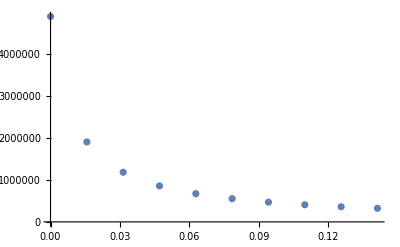

```mathematica
ListPlot[a, PlotRange->All]
```

```mathematica
a
```

{{0.,4.9×10^6},{0.03925,995074.},{0.0785,553747.},{0.11775,383608.}}